```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

## Parameters

```mathematica
(*Approximations: complexes are in equilibrium, effectors are conserved.

 r+t <-->C
t+e --> (te)b-->e
c+e --> (ce)b-->a+e
*)
```

```mathematica
(*effector interference mechanism 1: e2 degrades t1*)
```

```mathematica
gT=10; (*t growth*)
gR=1; (*NLR growth*)
deltaT=1; (*t decay*)
deltaR=1; (*NLR decay*)
beta1=1; (*effector-target affinity*)
beta2=1; (*effector-target unbinding*)
```

```mathematica
alphaF=0.5; (*R-T complex formation*)
alphaB=1; (*R-T complex unbinding*)
gamma1=1; (*complex-effector binding*)
gamma2=5; (*complex-effector unbinding*)
```

## Equations

```mathematica
(*solve for E based on e0 and quasi-equilibrium*)
```

```mathematica
fixedEEq=x+(beta1/beta2)*tVar*x+(gamma1/gamma2)*rVar*tVar*x*alphaF/(alphaB+gamma1*x)-e0Var==0;
fixedSol=x/.Solve[fixedEEq,x];
getE[thisR_?NumericQ,thisT_?NumericQ,thisE0_?NumericQ]:=Module[{numericSol,final},

numericSol=fixedSol/.{rVar->thisR,tVar->thisT,e0Var->thisE0}//N;
Sort[numericSol];
If[(numericSol[[1]]<0)&&(numericSol[[2]]>0),final=numericSol[[2]],final="error"];
final
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*get e2*)
```

```mathematica
getE2[e20Var_,tVar_]:=e20Var/(1+(beta1/beta2)*tVar);
```

```mathematica
getZ[eVar_]:=Module[{thisZ},
(* return Z*)
thisZ=eVar*alphaF*gamma1/(alphaB+gamma1*eVar);
thisZ
]
```

```mathematica
(*current r, t, a, then E0, beta1, gamma1*)
drds[rVar_,tVar_,aVar_,e0Var_]:=Module[{thisE,thisZ},

thisE=getE[rVar,tVar,e0Var];
thisZ=getZ[thisE];
gR-deltaR*rVar-rVar*tVar*thisZ+f[aVar]
]
```

```mathematica
dtds[rVar_,tVar_,e0Var_,e20Var_]:=Module[{thisE,thisZ,thisE2},
thisE=getE[rVar,tVar,e0Var];
thisE2=getE2[e20Var,tVar];
thisZ=getZ[thisE];
gT-deltaT*tVar-rVar*tVar*thisZ-beta1*tVar*(thisE+thisE2)
]
```

```mathematica
dads[rVar_,tVar_,aVar_,e0Var_]:=Module[{thisE,thisZ},

thisE=getE[rVar,tVar,e0Var];
thisZ=getZ[thisE];
rVar*tVar*thisZ-deltaR*aVar
]
(*dads=r[s]*t[s]*e*z;*)
```

```mathematica
f[z_]:=z^2;(*feedback*)
```

## solve and plot

```mathematica
ic={10,10,0}; (*initial amounts of r, t, a*)
tF=20;
testE0=3;
testE20=5;
sol=NDSolveValue[{r'[s]==drds[r[s],t[s],a[s],testE0],t'[s]==dtds[r[s],t[s],testE0,testE20],a'[s]==dads[r[s],t[s],a[s],testE0],r[0]==ic[[1]],t[0]==ic[[2]],a[0]==ic[[3]]},{r,t,a},{s,0,tF}]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
{rSol,tSol,aSol}=sol;
```

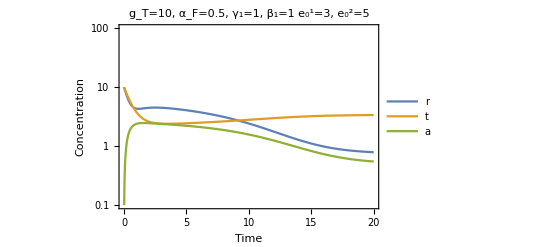

```mathematica
LogPlot[{rSol[s],tSol[s],aSol[s]},{s,0,tF},PlotLegends->{"r","t","a","e"},PlotLabel->"g_T="<>ToString[gT]<>", α_F="<>ToString[alphaF]<>", γ_1="<>ToString[gamma1]<>", β_1="<>ToString[beta1]<>"\n e_0^1="<>ToString[testE0]<>", e_0^2="<>ToString[testE20],PlotRange->{Automatic,{0.1,100}},LabelStyle->Directive[Black, 12],Frame->{True,True,False,False},FrameLabel->{"Time","Concentration"}]
```

## solver

```mathematica
(* remove duplicates *)
processRoots[rootList_]:=Module[{cleanList,test,unique,thisDist,i,j},
cleanList={rootList[[1]]};
For[i=2,i<=Length[rootList],i++,

test=rootList[[i]];
unique=True;
For[j=1,j<=Length[cleanList],j++,
	thisDist=EuclideanDistance[test,cleanList[[j]]];
	If[thisDist<10^-5,unique=False];
];
If[unique==True,AppendTo[cleanList,test];];

];

cleanList
]
```

```mathematica
getFixedPoint[e10Var_,e20Var_]:=Module[{rootList,thisSol,thisGuess,guessList,cleanList,i,j,k},
Print[e10Var];
guessList={0.1,1,10,100};
rootList={};
(*Print[e10Var];*)
For[i=1,i<=Length[guessList],i++,
For[j=1,j<=Length[guessList],j++,
For[k=1,k<=Length[guessList],k++,

thisSol=FindRoot[{drds[rVar,tVar,aVar,e10Var]==0,dtds[rVar,tVar,e10Var,e20Var]==0,dads[rVar,tVar,aVar,e10Var]==0},{rVar,guessList[[i]],0,10^6},{tVar,guessList[[j]],0,10^6},{aVar,guessList[[k]],0,10^6}];
residual=(drds[rVar,tVar,aVar,e10Var])^2+(dtds[rVar,tVar,e10Var,e20Var])^2+(dads[rVar,tVar,aVar,e10Var])^2/.thisSol; (*check convergence*)
If[residual<=10^-6,AppendTo[rootList,{rVar,tVar,aVar}/.thisSol];];
];
];
];
cleanList=processRoots[rootList];
cleanList
]
```

```mathematica
(*(e,list of fixed points)*)
rootsE20=1.1;
fixedPointList=Table[{i,getFixedPoint[i,rootsE20]},{i,0,20,.1}];
```

0.

FindRoot::nlnum: The function value {0.91-(0.005 error)/(1.+error),9.9-(0.005 error)/(1.+error)-0.1 (1.+error),-0.1+(0.005 error)/(1.+error)} is not a list of numbers with dimensions {3} at {rVar,tVar,aVar} = {0.1,0.1,0.1}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[{drds[rVar,tVar,aVar,0.]==0,dtds[rVar,tVar,0.,1.1]==0,dads[rVar,tVar,aVar,0.]==0},{rVar,guessList$12127188⟦i$12127188⟧,0,10^6},{tVar,guessList$12127188⟦j$12127188⟧,0,10^6},{aVar,guessList$12127188⟦k$12127188⟧,0,10^6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

0.1

FindRoot::reged: The point {0.,0.104782,9.99027} is at the edge of the search region {0.,1.×10^6} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.,0.100213,99.9994} is at the edge of the search region {0.,1.×10^6} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.,1.00524,9.99207} is at the edge of the search region {0.,1.×10^6} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

0.2

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.3

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

0.4

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.5

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

0.6

0.7

0.8

0.9

1.

1.1

1.2

1.3

1.4

1.5

1.6

1.7

1.8

1.9

2.

2.1

2.2

2.3

2.4

2.5

2.6

2.7

2.8

2.9

3.

3.1

3.2

3.3

3.4

3.5

3.6

3.7

3.8

3.9

4.

4.1

4.2

4.3

4.4

4.5

4.6

4.7

4.8

4.9

5.

5.1

5.2

5.3

5.4

5.5

5.6

5.7

5.8

5.9

6.

6.1

6.2

6.3

6.4

6.5

6.6

6.7

6.8

6.9

7.

7.1

7.2

7.3

7.4

7.5

7.6

7.7

7.8

7.9

8.

8.1

8.2

8.3

8.4

8.5

8.6

8.7

8.8

8.9

9.

9.1

9.2

9.3

9.4

9.5

9.6

9.7

9.8

9.9

10.

10.1

10.2

10.3

10.4

10.5

10.6

10.7

10.8

10.9

11.

11.1

11.2

11.3

11.4

11.5

11.6

11.7

11.8

11.9

12.

12.1

12.2

12.3

12.4

12.5

12.6

12.7

12.8

12.9

13.

13.1

13.2

13.3

13.4

13.5

13.6

13.7

13.8

13.9

14.

14.1

14.2

14.3

14.4

14.5

14.6

14.7

14.8

14.9

15.

15.1

15.2

15.3

15.4

15.5

15.6

15.7

15.8

15.9

16.

16.1

16.2

16.3

16.4

16.5

16.6

16.7

16.8

16.9

17.

17.1

17.2

17.3

17.4

17.5

17.6

17.7

17.8

17.9

18.

18.1

18.2

18.3

18.4

18.5

18.6

18.7

18.8

18.9

19.

19.1

19.2

19.3

19.4

19.5

19.6

19.7

19.8

19.9

20.

```mathematica
(*convert a list where each e has a 3D ss, to coordinates for plotting. want r*(e), t*(e), a*(e)*)
getPlottingCoords[fixedPoints_]:=Module[{},

rPoints={};
tPoints={};
aPoints={};

For[i=1,i<=Length[fixedPoints],i++,

thisPoint=fixedPoints[[i]];
eValue=thisPoint[[1]];

For[j=1,j<=Length[thisPoint[[2]]],j++,

thisFixedPoint=thisPoint[[2,j]];
AppendTo[rPoints,{eValue,thisFixedPoint[[1]]}];
AppendTo[tPoints,{eValue,thisFixedPoint[[2]]}];
AppendTo[aPoints,{eValue,thisFixedPoint[[3]]}];
];
];

{rPoints,tPoints,aPoints}

]
```

```mathematica
{rCoords,tCoords,aCoords}=getPlottingCoords[fixedPointList];
```

Part::partw: Part 3 of {}⟦1⟧ does not exist.

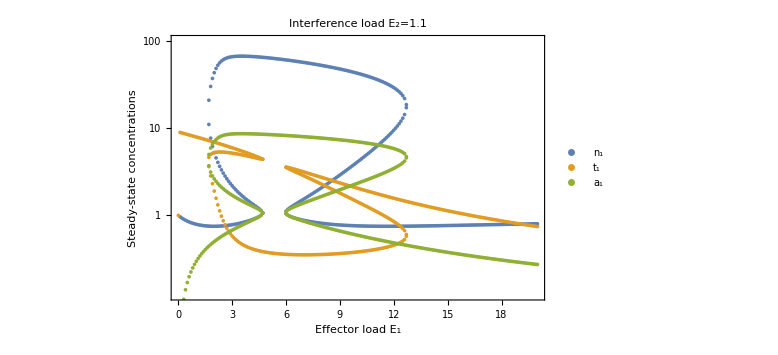

```mathematica
bifurcationPlot=ListLogPlot[{rCoords,tCoords,aCoords},PlotRange->{Automatic,{0,100}},PlotLabel->"Interference load E_2="<>ToString[rootsE20],FrameLabel->{"Effector load E_1","Steady-state concentrations"},LabelStyle->Directive[Black, 20],PlotLegends->{"n_1","t_1","a_1"},Frame->{True,True,False,False},ImageSize->Large]
```

```mathematica
(*Export["inteferencePoints_e2_"<>ToString[rootsE20]<>"_rta.mx",{rCoords,tCoords,aCoords}]*)
```

inteferencePoints_e2_1.1_rta.mx

```mathematica
(*Export["interference_mech1_bifurcation_E2_"<>ToString[rootsE20]<>".png",%,ImageResolution->200]*)
```